## Derivation of Diffusion and Advection

#### Jinghao Chen jinghc2@uci.edu

Taylor expansions of cell density functions:

```mathematica
rur= r+h (rx+ry)+h^2/2 (rxx+ryy+2 rxx ryy)+HOT;(*up right*)
rdr=r+h (rx-ry)+h^2/2 (rxx+ryy-2 rxx ryy)+HOT;(*down right*)
rul=r+h (-rx+ry)+h^2/2 (rxx+ryy-2 rxx ryy)+HOT;(*up left*)
rdl=r-h (rx+ry)+h^2/2 (rxx+ryy+2 rxx ryy)+HOT;(*down left*)
```

where rur, rdr, rul, rdl are cell densities at up right, down right, up left and down left corners, respectively, with expansions around the central point. rx and ry are partial derivatives of cell density w.r.t spatial variable x and y, while rxx and ryy are corresponding second order derivatives. h is the grid size, HOT represents a “higher order term”, i.e., in O(h^3).

#### Diffusion, with isotropic diffusivity for simplification:

```mathematica
DIF = 1/h^2((1-r)(1-a (r-2 h rx+2 h^2 rxx+HOT)) (1-a rul) (1-a rdl) (r-h rx +h^2/2 rxx +HOT)^2+ (1-r)(1-a (r+2 h rx+2 h^2 rxx+HOT)) (1-a rur) (1-a rdr) (r+h rx +h^2/2 rxx +HOT)^2+(1-r)(1-a (r-2 h ry+2 h^2 ryy+HOT)) (1-a rdl) (1-a rdr) (r-h ry +h^2/2 ryy +HOT)^2+ (1-r)(1-a (r+2 h ry+2 h^2 ryy+HOT)) (1-a rul) (1-a rur) (r+h ry +h^2/2 ryy +HOT)^2-(1-(r+h rx +h^2/2 rxx +HOT)) (1-a (r-h rx +h^2/2 rxx +HOT)) (1-a (r-h ry +h^2/2 ryy +HOT)) (1-a (r+h ry +h^2/2 ryy +HOT)) r^2-(1-(r-h rx +h^2/2 rxx +HOT)) (1-a (r+h rx +h^2/2 rxx +HOT)) (1-a (r-h ry +h^2/2 ryy +HOT)) (1-a (r+h ry +h^2/2 ryy +HOT)) r^2-(1-(r+h ry +h^2/2 ryy +HOT)) (1-a (r-h ry +h^2/2 ryy +HOT)) (1-a (r-h rx +h^2/2 rxx +HOT)) (1-a (r+h rx +h^2/2 rxx +HOT)) r^2-(1-(r-h ry +h^2/2 ryy +HOT)) (1-a (r+h ry +h^2/2 ryy +HOT)) (1-a (r-h rx +h^2/2 rxx +HOT)) (1-a (r+h rx +h^2/2 rxx +HOT)) r^2);
Expand[Limit[Limit[DIF,HOT->0],h->0]]
```

2 rx^2-2 r rx^2-22 a r rx^2+24 a r^2 rx^2+48 a^2 r^2 rx^2-52 a^2 r^3 rx^2-28 a^3 r^3 rx^2+30 a^3 r^4 rx^2+2 r rxx-r^2 rxx-11 a r^2 rxx+8 a r^3 rxx+16 a^2 r^3 rxx-13 a^2 r^4 rxx-7 a^3 r^4 rxx+6 a^3 r^5 rxx+2 ry^2-2 r ry^2-22 a r ry^2+24 a r^2 ry^2+48 a^2 r^2 ry^2-52 a^2 r^3 ry^2-28 a^3 r^3 ry^2+30 a^3 r^4 ry^2+2 r ryy-r^2 ryy-11 a r^2 ryy+8 a r^3 ryy+16 a^2 r^3 ryy-13 a^2 r^4 ryy-7 a^3 r^4 ryy+6 a^3 r^5 ryy

where a is alpha, the cell-cell adhesion coefficient in the model. We can extract the scalar diffusion coefficient from above, and check the positive definite diffusivity area:

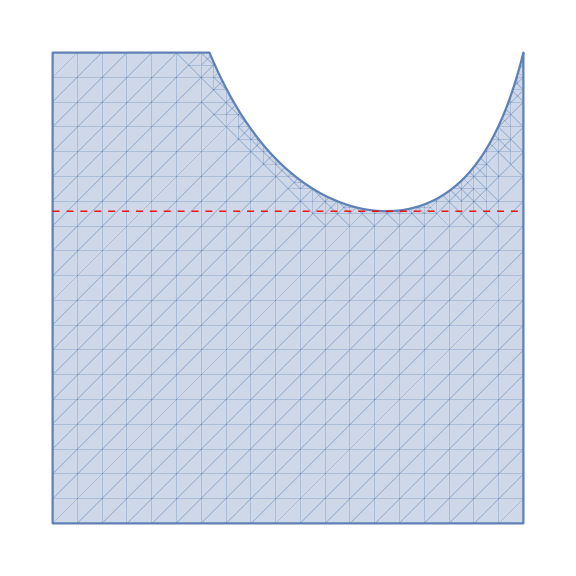

```mathematica
p1=Show[RegionPlot[Reduce[{2-(1+11 a) r+(8 a+16 a^2) r^2-(13 a^2+7 a^3) r^3+6 a^3 r^4>=0}],{r,0,1},{a,0,1}],Frame->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[Medium]],FrameLabel->{{HoldForm[adhesion coefficient α],None},{HoldForm[cell density ρ],None}},ImageSize->Large,LabelStyle->{18,GrayLevel[0]}];
p2=Plot[1/(17-4 Sqrt[15]),{x,0,1},PlotStyle->{Dashed,Red,Thick}];
Show[p1,p2]
```

#### Advection, modeling the retraction, without temporal periodicity for simplification:

```mathematica
ADV= 1/h((1-a (r-2 h rx+2 h^2 rxx+HOT)) (1-a rul) (1-a rdl) (r-h rx +h^2/2 rxx +HOT)(br-h brx+h^2/2 brxx)+ (1-a (r+2 h rx+2 h^2 rxx+HOT)) (1-a rur) (1-a rdr) (r+h rx +h^2/2 rxx +HOT)(bl+h blx+h^2/2 blxx)+(1-a (r-2 h ry+2 h^2 ryy+HOT)) (1-a rdl) (1-a rdr) (r-h ry +h^2/2 ryy +HOT)(bu-h buy+h^2/2 buyy)+ (1-a (r+2 h ry+2 h^2 ryy+HOT)) (1-a rul) (1-a rur) (r+h ry +h^2/2 ryy +HOT)(bd+h bdy+h^2/2 bdyy)- (1-a (r-h rx +h^2/2 rxx +HOT)) (1-a (r-h ry +h^2/2 ryy +HOT)) (1-a (r+h ry +h^2/2 ryy +HOT)) r br- (1-a (r+h rx +h^2/2 rxx +HOT)) (1-a (r-h ry +h^2/2 ryy +HOT)) (1-a (r+h ry +h^2/2 ryy +HOT)) r bl- (1-a (r-h ry +h^2/2 ryy +HOT)) (1-a (r-h rx +h^2/2 rxx +HOT)) (1-a (r+h rx +h^2/2 rxx +HOT)) r bu- (1-a (r+h ry +h^2/2 ryy +HOT)) (1-a (r-h rx +h^2/2 rxx +HOT)) (1-a (r+h rx +h^2/2 rxx +HOT)) r bd);
Simplify[Limit[Limit[ADV,HOT->0],h->0]]
```

-(-1+a r)^2 (brx r+buy r-a brx r^2-a buy r^2+bdy r (-1+a r)+blx r (-1+a r)-bl rx+br rx+4 a bl r rx-4 a br r rx-bd ry+bu ry+4 a bd r ry-4 a bu r ry)

where bl, br, bu, bd are Delta r in the model with sup-scripts arrows to the left, right, up and down directionss.